0.9

0.6

0.5

0.644471

0.025

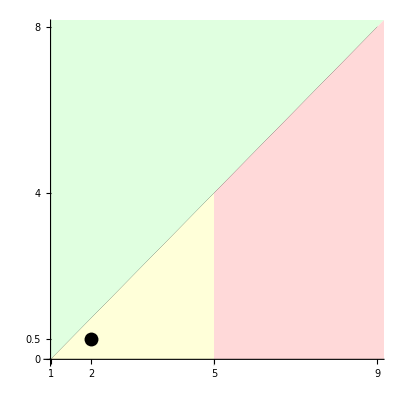

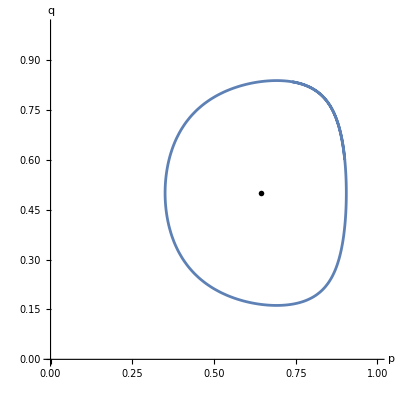

-Graphics-

-Graphics-

-Graphics-

```mathematica
ClearAll["Global`*"]

(*the payoff functions*)
GainVD=HeavisideTheta[(1-p[t])*q[t]-extinctThreshold]*((1-p[t]^n)*bv/((1-p[t])*(n+1))-c);
GainG=HeavisideTheta[p[t]-extinctThreshold]*(ba/(n+1)-HeavisideTheta[(1-p[t])*q[t]-extinctThreshold]*(q[t] (bv-c))-treatG[t]);

(*some concrete numbers for simulation*)

tsecond=3;
tmax=30;

pin=0.9
qin=0.6

n=4;
c=1;

bv=2*c;
ba=0.5*c*(n+1);

extinctThreshold=10^(-4);
therapyStrength=3*c;

(*Find the location of the internal eq*)
qcenter=(ba)/((bv-c)*(n+1))
pcenter=x/. FindRoot[(1-x^(n+1))*bv==c (n+1)*(1-x),{x,1-bv/(c*(n+1))}]

(*Plot the parameter values*)
dotSize=0.025

Show[Plot[x-c,{x,c,2*c (n+1)},PlotRange->{{c,2*c (n+1)-c},{0,2*c*n}},GridLines->{{c*(n+1)},{}},PlotStyle->Black,AspectRatio->1,AxesOrigin->{c,0},Ticks->{{c,bv,c (n+1),2*c (n+1)-c},{0,ba/(n+1),c*n,2*c*n}}],Graphics[{LightYellow,Polygon[{{c,0},{c (n+1),0},{c (n+1),c (n+1)-c}}]}],Graphics[{LightGreen,Polygon[{{c,0},{c,2*c (n+1)-c},{2*c (n+1),2*c (n+1)-c}}]}],Graphics[{LightRed,Polygon[{{c (n+1),0},{c (n+1),c (n+1)-c},{2*c (n+1),2*c (n+1)-c},{2*c (n+1),0}}]}],Graphics[{Black,PointSize[dotSize],Point[{bv,ba/(n+1)}]}]]

(*Solve the dynamics*)
treatG[t]=0;

solMod=NDSolve[{p'[t]==Simplify[p[t]*(1-p[t])*GainG],q'[t]==Simplify[q[t]*(1-q[t])*GainVD],p[0]==pin,q[0]==qin},{p[t],q[t]},{t,0,tmax}];

Show[ParametricPlot[{p[t],q[t]}/. solMod,{t,0,tmax},PlotRange->{{0,1},{0,1}},AxesLabel->{"p","q"}],Graphics[{PointSize[0.01],Point[{pcenter,qcenter}]}]]

fig0=Plot[Evaluate[{p[t],q[t],(1-p[t])*q[t],(1-p[t])*(1-q[t])}/. solMod],{t,0,tmax},PlotRange->{{0,tmax},{0,1}},GridLines->{{},{}},PlotStyle->{Green,{Red,Dashed},Red,Blue},Ticks->{{0,tmax},{0,qin,pin,1}},AspectRatio->1/3,PlotLabels->{"GLY",None,"VOP", "DEF"}]


(*Plot targetting GLY*)
treatG[t]=therapyStrength*(1-1*HeavisideTheta[t-tsecond]);

solMod1=NDSolve[{p'[t]==Simplify[p[t]*(1-p[t])*GainG],q'[t]==Simplify[q[t]*(1-q[t])*GainVD],p[0]==pin,q[0]==qin},{p[t],q[t]},{t,0,tmax}];

(*Show[ParametricPlot[{p[t],q[t]}/.solMod1,{t,0,tsecond},PlotRange->{{0,1},{0,1}},AxesLabel->{"p","q"},PlotStyle->{Gray}],ParametricPlot[{p[t],q[t]}/.solMod1,{t,tsecond,tmax},PlotRange->{{0,1},{0,1}},AxesLabel->{"p","q"}],Graphics[{PointSize[0.01],Point[{pcenter,qcenter}]}]]*)

(*plot the dynamics of p=x_G,q,x_V,x_D*)
fig1=Plot[Evaluate[{p[t],q[t],(1-p[t])*q[t],(1-p[t])*(1-q[t])}/. solMod1],{t,0,tmax},PlotRange->{{0,tmax},{0,1}},GridLines->{{tsecond},{}},PlotStyle->{Green,{Red,Dashed},Red,Blue},Ticks->{{0,tsecond,tmax},{0,qin,pin,1}},AspectRatio->1/3,PlotLabels->{"GLY",None,"VOP", "DEF"}];

full1=Show[fig1,Graphics[{LightGray,Polygon[{{0,0},{0,1},{tsecond,1},{tsecond,0}}]}],fig1]

(*Plot targetting GLY*)
tstart=10;
tend=tstart+tsecond;
treatG[t]=therapyStrength*(HeavisideTheta[t-tstart]-HeavisideTheta[t-tend]);

solMod2=NDSolve[{p'[t]==Simplify[p[t]*(1-p[t])*GainG],q'[t]==Simplify[q[t]*(1-q[t])*GainVD],p[0]==pin,q[0]==qin},{p[t],q[t]},{t,0,tmax}];

(*Show[ParametricPlot[{p[t],q[t]}/.solMod2,{t,0,tstart},PlotRange->{{0,1},{0,1}},AxesLabel->{"p","q"}],ParametricPlot[{p[t],q[t]}/.solMod2,{t,tstart,tend},PlotRange->{{0,1},{0,1}},AxesLabel->{"p","q"},PlotStyle->{Gray}],ParametricPlot[{p[t],q[t]}/.solMod2,{t,tend,tmax},PlotRange->{{0,1},{0,1}},AxesLabel->{"p","q"}],Graphics[{PointSize[0.01],Point[{pcenter,qcenter}]}]]*)

(*plot the dynamics of p=x_G,q,x_V,x_D*)
fig2=Plot[Evaluate[{p[t],q[t],(1-p[t])*q[t],(1-p[t])*(1-q[t])}/. solMod2],{t,0,tmax},PlotRange->{{0,tmax},{0,1}},GridLines->{{tstart,tend},{}},PlotStyle->{Green,{Red,Dashed},Red,Blue},Ticks->{{0,tstart,tend,tmax},{0,qin,pin,1}},AspectRatio->1/3,PlotLabels->{"GLY",None,"VOP", "DEF"}];

full2=Show[fig2,Graphics[{LightGray,Polygon[{{tstart,0},{tstart,1},{tend,1},{tend,0}}]}],fig2]
```